Your Title Here

```mathematica
(*saturated liquid*)
```

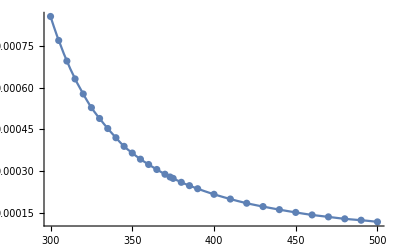

```mathematica
μL=Quiet@Interpolation[{{300.,0.000855},{305.,0.0007689},{310.,0.000695},{315.,0.0006309},{320.,0.0005769},{325.,0.0005279},{330.,0.000489},{335.,0.000453},{340.,0.00041996},{345.,0.00038897},{350.,0.000365},{355.,0.000343},{360.,0.00032396},{365.,0.000306},{370.,0.000289},{373.15,0.000279},{375.,0.000274},{380.,0.00026},{385.,0.000248},{390.,0.000237},{400.,0.000217},{410.,0.00019998},{420.,0.000185},{430.,0.000173},{440.,0.00016198},{450.,0.00015198},{460.,0.000143},{470.,0.000136},{480.,0.000129},{490.,0.000124},{500.,0.000118}}];(*N s/m2*)

Show[Plot[μL[x],{x,300,500}],ListPlot[{{300.,0.000855},{305.,0.0007689},{310.,0.000695},{315.,0.0006309},{320.,0.0005769},{325.,0.0005279},{330.,0.000489},{335.,0.000453},{340.,0.00041996},{345.,0.00038897},{350.,0.000365},{355.,0.000343},{360.,0.00032396},{365.,0.000306},{370.,0.000289},{373.15,0.000279},{375.,0.000274},{380.,0.00026},{385.,0.000248},{390.,0.000237},{400.,0.000217},{410.,0.00019998},{420.,0.000185},{430.,0.000173},{440.,0.00016198},{450.,0.00015198},{460.,0.000143},{470.,0.000136},{480.,0.000129},{490.,0.000124},{500.,0.000118}}]]
```

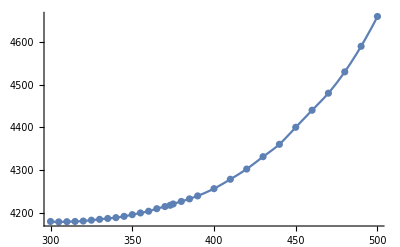

```mathematica
CpL=Quiet@Interpolation[{#1,1000*#2}&@@@{{300.,4.179},{305.,4.178},{310.,4.1785},{315.,4.179},{320.,4.180},{325.,4.182},{330.,4.184},{335.,4.186},{340.,4.188},{345.,4.191},{350.,4.195},{355.,4.199},{360.,4.203},{365.,4.209},{370.,4.214},{373.15,4.217},{375.,4.220},{380.,4.226},{385.,4.232},{390.,4.239},{400.,4.256},{410.,4.278},{420.,4.302},{430.,4.331},{440.,4.36},{450.,4.4},{460.,4.44},{470.,4.48},{480.,4.53},{490.,4.59},{500.,4.66}}];(*kJ/kg/K*)

Show[Plot[CpL[x],{x,300,500}],ListPlot[{#1,1000*#2}&@@@{{300.,4.179},{305.,4.178},{310.,4.1785},{315.,4.179},{320.,4.180},{325.,4.182},{330.,4.184},{335.,4.186},{340.,4.188},{345.,4.191},{350.,4.195},{355.,4.199},{360.,4.203},{365.,4.209},{370.,4.214},{373.15,4.217},{375.,4.220},{380.,4.226},{385.,4.232},{390.,4.239},{400.,4.256},{410.,4.278},{420.,4.302},{430.,4.331},{440.,4.36},{450.,4.4},{460.,4.44},{470.,4.48},{480.,4.53},{490.,4.59},{500.,4.66}}]]
```

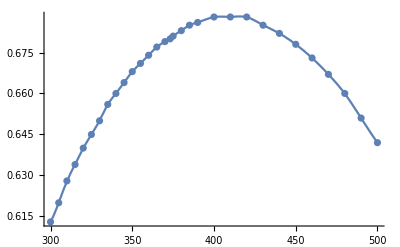

```mathematica
kL=Quiet@Interpolation@{{300.,0.6130},{305.,0.62},{310.,0.628},{315.,0.634},{320.,0.64},{325.,0.645},{330.,0.65},{335.,0.656},{340.,0.66},{345.,0.664},{350.,0.668},{355.,0.671},{360.,0.674},{365.,0.677},{370.,0.679},{373.15,0.68},{375.,0.681},{380.,0.683},{385.,0.685},{390.,0.686},{400.,0.6880},{410.,0.6880},{420.,0.6880},{430.,0.685},{440.,0.682},{450.,0.678},{460.,0.673},{470.,0.667},{480.,0.66001},{490.,0.651},{500.,0.642}};(*W/m/K*)

Show[Plot[kL[x],{x,300,500}],ListPlot[{{300.,0.6130},{305.,0.62},{310.,0.628},{315.,0.634},{320.,0.64},{325.,0.645},{330.,0.65},{335.,0.656},{340.,0.66},{345.,0.664},{350.,0.668},{355.,0.671},{360.,0.674},{365.,0.677},{370.,0.679},{373.15,0.68},{375.,0.681},{380.,0.683},{385.,0.685},{390.,0.686},{400.,0.6880},{410.,0.6880},{420.,0.6880},{430.,0.685},{440.,0.682},{450.,0.678},{460.,0.673},{470.,0.667},{480.,0.66001},{490.,0.651},{500.,0.642}}]]
```

```mathematica
(*steam*)
```

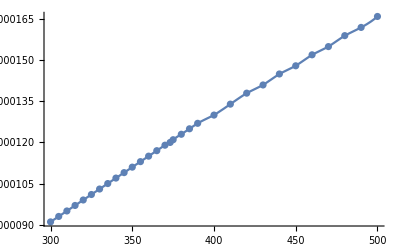

```mathematica
μS=Quiet@Interpolation@{{300.,9.1*^-6},{305.,9.299*^-6},{310.,9.499*^-6},{315.,9.7*^-6},{320.,9.9*^-6},{325.,0.0000101},{330.,0.0000103},{335.,0.0000105},{340.,0.0000107},{345.,0.000010899},{350.,0.000011099},{355.,0.0000113},{360.,0.0000115},{365.,0.0000117},{370.,0.0000119},{373.15,0.000012},{375.,0.0000121},{380.,0.000012299},{385.,0.000012499},{390.,0.000012699},{400.,0.000013},{410.,0.000013399},{420.,0.0000138},{430.,0.000014099},{440.,0.0000145},{450.,0.000014799},{460.,0.0000152},{470.,0.0000155},{480.,0.0000159},{490.,0.0000162},{500.,0.0000166}};

Show[Plot[μS[x],{x,300,500}],ListPlot[{{300.,9.1*^-6},{305.,9.299*^-6},{310.,9.499*^-6},{315.,9.7*^-6},{320.,9.9*^-6},{325.,0.0000101},{330.,0.0000103},{335.,0.0000105},{340.,0.0000107},{345.,0.000010899},{350.,0.000011099},{355.,0.0000113},{360.,0.0000115},{365.,0.0000117},{370.,0.0000119},{373.15,0.000012},{375.,0.0000121},{380.,0.000012299},{385.,0.000012499},{390.,0.000012699},{400.,0.000013},{410.,0.000013399},{420.,0.0000138},{430.,0.000014099},{440.,0.0000145},{450.,0.000014799},{460.,0.0000152},{470.,0.0000155},{480.,0.0000159},{490.,0.0000162},{500.,0.0000166}}]]
```

```mathematica
N@134*^-7
```

0.0000134

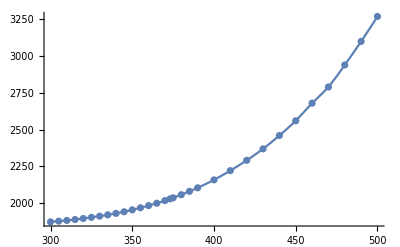

```mathematica
CpS=Quiet@Interpolation[{#1,1000*#2}&@@@{{300.,1.872},{305.,1.877},{310.,1.8820},{315.,1.8880},{320.,1.895},{325.,1.903},{330.,1.911},{335.,1.92},{340.,1.93},{345.,1.941},{350.,1.954},{355.,1.968},{360.,1.983},{365.,1.999},{370.,2.017},{373.15,2.029},{375.,2.036},{380.,2.057},{385.,2.08},{390.,2.104},{400.,2.158},{410.,2.221},{420.,2.291},{430.,2.369},{440.,2.46},{450.,2.56},{460.,2.68},{470.,2.79},{480.,2.94},{490.,3.1},{500.,3.27}}];

Show[Plot[CpS[x],{x,300,500}],ListPlot[{#1,1000*#2}&@@@{{300.,1.872},{305.,1.877},{310.,1.8820},{315.,1.8880},{320.,1.895},{325.,1.903},{330.,1.911},{335.,1.92},{340.,1.93},{345.,1.941},{350.,1.954},{355.,1.968},{360.,1.983},{365.,1.999},{370.,2.017},{373.15,2.029},{375.,2.036},{380.,2.057},{385.,2.08},{390.,2.104},{400.,2.158},{410.,2.221},{420.,2.291},{430.,2.369},{440.,2.46},{450.,2.56},{460.,2.68},{470.,2.79},{480.,2.94},{490.,3.1},{500.,3.27}}]]
```

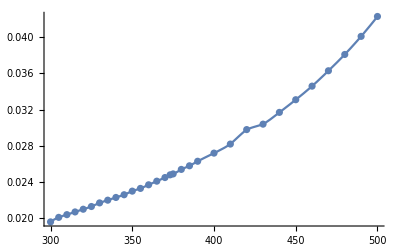

```mathematica
kS=Quiet@Interpolation@{{300.,0.0196},{305.,0.0201},{310.,0.0204},{315.,0.0207},{320.,0.021},{325.,0.0213},{330.,0.0217},{335.,0.0220},{340.,0.0223},{345.,0.0226},{350.,0.023},{355.,0.0233},{360.,0.0237},{365.,0.0241},{370.,0.0245},{373.15,0.024800},{375.,0.0249},{380.,0.0254},{385.,0.0258},{390.,0.0263},{400.,0.0272},{410.,0.028200},{420.,0.0298},{430.,0.0304},{440.,0.0317},{450.,0.0331},{460.,0.0346},{470.,0.0363},{480.,0.0381},{490.,0.0401},{500.,0.0423}};

Show[Plot[kS[x],{x,300,500}],ListPlot[{{300.,0.0196},{305.,0.0201},{310.,0.0204},{315.,0.0207},{320.,0.021},{325.,0.0213},{330.,0.0217},{335.,0.0220},{340.,0.0223},{345.,0.0226},{350.,0.023},{355.,0.0233},{360.,0.0237},{365.,0.0241},{370.,0.0245},{373.15,0.024800},{375.,0.0249},{380.,0.0254},{385.,0.0258},{390.,0.0263},{400.,0.0272},{410.,0.028200},{420.,0.0298},{430.,0.0304},{440.,0.0317},{450.,0.0331},{460.,0.0346},{470.,0.0363},{480.,0.0381},{490.,0.0401},{500.,0.0423}}]]
```

```mathematica
(*sodium*)
```

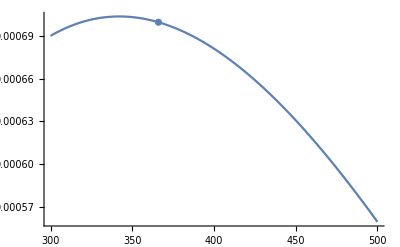

```mathematica
μNa=Quiet@Interpolation@{{300,0.0006904},{366.,0.0007},{644.,0.00030000},{977.,0.0002}};

Show[Plot[μNa[x],{x,300,500}],ListPlot[{{366.,0.0007},{644.,0.00030000},{977.,0.0002}}]]
```

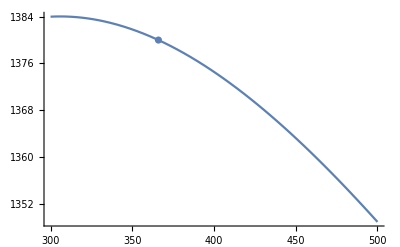

```mathematica
CpNa=Quiet@Interpolation[{#1,1000*#2}&@@@{{300,1.384},{366.,1.3800},{644.,1.3},{977.,1.26}}];

Show[Plot[CpNa[x],{x,300,500}],ListPlot[{#1,1000*#2}&@@@{{366.,1.3800},{644.,1.3},{977.,1.26}}]]
```

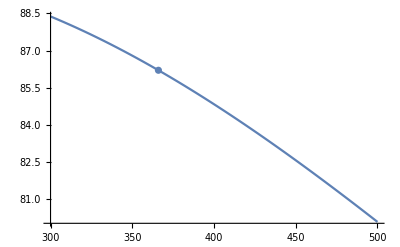

```mathematica
kNa=Quiet@Interpolation@{{300,88.38},{366.,86.2},{644.,72.3},{977.,59.7}};

Show[Plot[kNa[x],{x,300,500}],ListPlot[{{366.,86.2},{644.,72.3},{977.,59.7}}]]
```

```mathematica
(*oil, unused engine oil*)
```

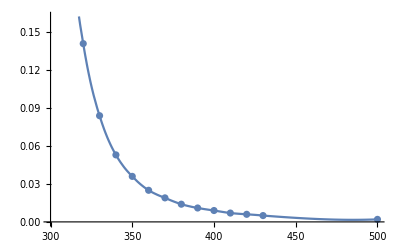

```mathematica
μO=Quiet@Interpolation@{{273.,3.85},{280.,2.17},{290.,0.999},{300.,0.486},{310.,0.253},{320.,0.14100},{330.,0.084},{340.,0.053},{350.,0.0360},{360.,0.025},{370.,0.019},{380.,0.014},{390.,0.011},{400.,0.009000},{410.,0.007},{420.,0.006},{430.,0.005},{500,0.002}};

Show[Plot[μO[x],{x,300,500}],ListPlot[{{273.,3.85},{280.,2.17},{290.,0.999},{300.,0.486},{310.,0.253},{320.,0.14100},{330.,0.084},{340.,0.053},{350.,0.0360},{360.,0.025},{370.,0.019},{380.,0.014},{390.,0.011},{400.,0.009000},{410.,0.007},{420.,0.006},{430.,0.005},{500,μO[500]}}]]
```

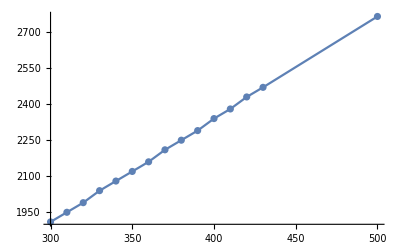

```mathematica
CpO=Quiet@Interpolation[{#1,1000*#2}&@@@{{273.,1.8},{280.,1.83},{290.,1.87},{300.,1.9100},{310.,1.95},{320.,1.99},{330.,2.04},{340.,2.08},{350.,2.12},{360.,2.16},{370.,2.21},{380.,2.25},{390.,2.29},{400.,2.34},{410.,2.38},{420.,2.43},{430.,2.47},{500,2.765}},InterpolationOrder->1];
Show[Plot[CpO[x],{x,300,500}],ListPlot[{#1,1000*#2}&@@@{{273.,1.8},{280.,1.83},{290.,1.87},{300.,1.9100},{310.,1.95},{320.,1.99},{330.,2.04},{340.,2.08},{350.,2.12},{360.,2.16},{370.,2.21},{380.,2.25},{390.,2.29},{400.,2.34},{410.,2.38},{420.,2.43},{430.,2.47},{500,2.765}}]]
```

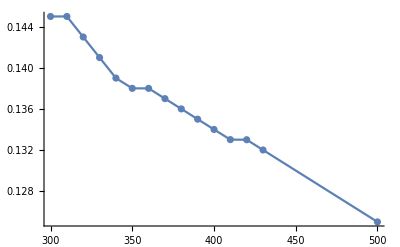

```mathematica
kO=Quiet@Interpolation[{{273.,0.147},{280.,0.144},{290.,0.145},{300.,0.145},{310.,0.145},{320.,0.143},{330.,0.14100},{340.,0.139},{350.,0.138},{360.,0.138},{370.,0.137},{380.,0.136},{390.,0.135},{400.,0.134},{410.,0.13301},{420.,0.133},{430.,0.132},{500,0.125}},InterpolationOrder->1];
Show[Plot[kO[x],{x,300,500}],ListPlot[{{273.,0.147},{280.,0.144},{290.,0.145},{300.,0.145},{310.,0.145},{320.,0.143},{330.,0.14100},{340.,0.139},{350.,0.138},{360.,0.138},{370.,0.137},{380.,0.136},{390.,0.135},{400.,0.134},{410.,0.13301},{420.,0.133},{430.,0.132},{500,0.125}}]]
```

```mathematica
Manipulate[
Module[{do,di,Th1,Tc1,d,m,μ,Cp,k,ReD,ho,hi,U,tc2,ΔT1,ΔT2,Th2,Tc2},
do=0.025;di=0.01;(*do=0.045;di=0.025;*)(*m*)
Th1=500;(*K*)
Tc1=300;
(*Th1=353;Tc1=35+273;*)

d[h]=do+di;m[h]=mh;
Switch[fluid,(*hot fluid*)
1,{μ[h]=μS[Th1];Cp[h]=CpS[Th1];k[h]=kS[Th1];},(*steam*)
2,{μ[h]=μL[Th1];Cp[h]=CpL[Th1];k[h]=kL[Th1];},(*liquid*)
3,{μ[h]=μNa[Th1];Cp[h]=CpNa[Th1];k[h]=kNa[Th1];},(*sodium*)
4,{μ[h]=μO[Th1];Cp[h]=CpO[Th1];k[h]=kO[Th1];}(*oil*)
];
d[c]=di;m[c]=mc;μ[c]=μL[Tc1];Cp[c]=CpL[Tc1];k[c]=kL[Tc1];(*cold, liquid*)

ReD[i_]:=m[i]/(π/4*d[i]*μ[i]);

ho=k[h]/d[h]*If[ReD[h]>10000,0.023*ReD[h]^(4/5)*((Cp[h]*μ[h])/k[h])^0.3,Quiet@Interpolation[{{0.05,4.06},{0.1,4.11},{0.25,4.23},{0.5,4.43},{1,4.86}}][di/do]];
hi=k[c]/d[c]*If[ReD[c]>10000,0.023*ReD[c]^(4/5)*((Cp[c]*μ[c])/k[c])^0.4,Quiet@Interpolation[{{0.05,17.46},{0.1,11.56},{0.25,7.37},{0.5,5.74},{1,4.86}},InterpolationOrder->1][di/do]];

U=(1/hi+1/ho)^-1;

tc2=tc/.Quiet@Solve[m[c]*Cp[c]*(tc-Tc1)==m[h]*Cp[h]*(Th1-th2),tc][[1]];

ΔT1=If[flow==1,Th1-Tc1,Th1-tc2];
ΔT2=If[flow==1,th2-tc2,th2-Tc1];

(*Th2=Quiet@Re[th2/.FindRoot[U*π*di*L*(ΔT1-ΔT2)/Log[ΔT1/ΔT2]==m[h]*Cp[h]*(Th1-th2),{th2,350}]];*)

Th2=th2/.Quiet@Solve[U*π*di*L*(ΔT1-ΔT2)/Log[ΔT1/ΔT2]==m[h]*Cp[h]*(Th1-th2),th2][[1]];
Tc2=tc2/.th2->Th2;

ListPlot[{{{0,Tc1},{L,Tc2}},{{0,Th1},{L,Th2}}},Joined->True]

(*Text@Style[Row[{
Grid[{{"T_(c, 1) =",Tc1},{"T_(c, 2) =",Tc2},{"ΔT_c =",Tc2-Tc1}}],Spacer[50],
Grid[{{"T_(h, 1) =",Th1},{"T_(h, 2) =",Th2},{"ΔT_h =",Th1-Th2}}]
}],17]*)
],
Row[{
Control[{{flow,1,"fluid flow:"},{1->" parallel ",2->" counter "},Setter}],Spacer[25],
Control[{{fluid,1,"hot fluid:"},{1->"steam",2->"liquid water",3->"liquid sodium",4->"oil"},PopupMenu}]}],
Control[{{L,1.5,"length (m)"},0.7,3,0.1,Appearance->"Labeled"}],
Row[{Style["hot and cold mass flow rates (kg/s):",Bold],Spacer[25],
Control[{{mh,3,"hot"},0.1,5,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{mc,1,"cold"},0.1,5,0.1,Appearance->"Labeled",ImageSize->Small}]}],
SaveDefinitions->True]
```





```mathematica
328700
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX